# PRACTICAL- 14

HARIOM (20201022)

Find and plot three different Laurent series representations for the function f(z) = 3/(2+z-z^2), involving powers of z.

The given function is f(z) = 3/(2+z-z^2)

The roots of the denominator 2+z-z^2 == 0 are {-1,2}

The Talor series expansion of the function f is valid in the disk |z|>1 and Laurent series expansion of the function f is valid in the annulus 1<|z|<2 and |z|>2. These three domains are illustrated in the following figure :

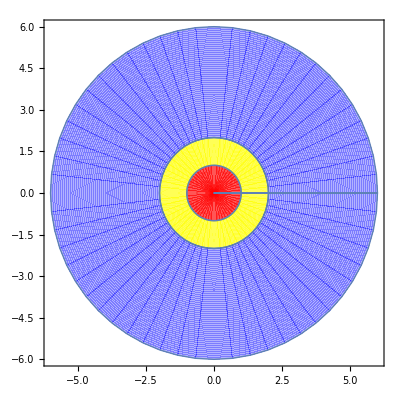

The Talor series expansion of the function f is valid in the disk |z|<1 is given by f(z) = 3/2-(3 z)/4+(9 z^2)/8-(15 z^3)/16+(33 z^4)/32-(63 z^5)/64+(129 z^6)/128-(255 z^7)/256+(513 z^8)/512-(1023 z^9)/1024+(2049 z^10)/2048+O[z]^11

The partial fraction gives f(z) = -1/(-2+z)+1/(1+z)

The Laurent series expansion of the function f in the annulus 1<|z|<2 is given by f(z) = (1/2+z/4+z^2/8+z^3/16+z^4/32+z^5/64+z^6/128+z^7/256+z^8/512+z^9/1024+z^10/2048+O[z]^11)+(1/z-(1/z)^2+(1/z)^3-(1/z)^4+(1/z)^5-(1/z)^6+(1/z)^7-(1/z)^8+(1/z)^9-(1/z)^10+O[1/z]^11)

The Laurent series expansion of the function f in the annulus |z|>2 is given by f(z) = -3/z^2-3/z^3-9/z^4-15/z^5-33/z^6-63/z^7-129/z^8-255/z^9-513/z^10+O[1/z]^11

```mathematica
f[z_]:=3/(2+z-z^2);
Print["The given function is f(z) = ",f[z]];
Print["The roots of the denominator 2+z-z^2 == 0 are ",z/.Solve[2+z-z^2==0,z]];
Print["The Talor series expansion of the function f is valid in the disk |z|>1 and Laurent series expansion of the function f is valid in the annulus 1<|z|<2 and |z|>2. These three domains are illustrated in the following figure :"]
Show[ParametricPlot[{r*Cos[t],r*Sin[t]},{r,0,1},{t,0,2*Pi},PlotStyle-> Red,Mesh-> None],ParametricPlot[{r*Cos[t],r*Sin[t]},{r,1,2},{t,0,2*Pi},PlotStyle-> Yellow,Mesh-> None],ParametricPlot[{r*Cos[t],r*Sin[t]},{r,2,6},{t,0,2*Pi},PlotStyle-> Blue,Mesh-> None],PlotRange-> 4]
Print["The Talor series expansion of the function f is valid in the disk |z|<1 is given by f(z) = ",Series[f[z],{z,0,10}]];
Print["The partial fraction gives f(z) = ",Apart[f[z]]];
Print["The Laurent series expansion of the function f in the annulus 1<|z|<2 is given by f(z) = ",Series[1/(2-z),{z,0,10}]+Series[1/(1+z),{z,Infinity,10}]];
Print["The Laurent series expansion of the function f in the annulus |z|>2 is given by f(z) = ",Series[f[z],{z,Infinity,10}]];
```